```mathematica
drawPerson[{x_, y_}] := {Black, Line[{{x, y}, {x+1, y+2}, {x+2, y}}], Line[{{x+1, y+2}, {x+1, y+4.5}}],Line[{{x,y+3.8},{x+2,y+3.8}}], Circle[{x+1, y+4.5+.5}, .5]}
```

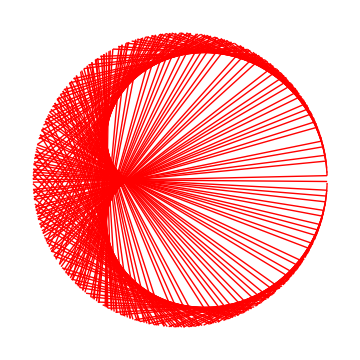

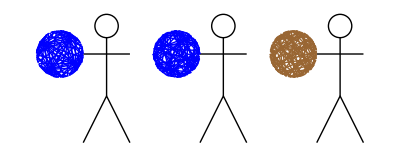

```mathematica
randColour[] := RandomChoice[{Red, Green, Blue, Cyan, Magenta, Black, Brown}];
randRadius[] := RandomChoice[{1,2,3}];
randThetaStep[] := RandomReal[{Pi/25, Pi}];

SpiroLines[{x_, y_, r_, stepT1_, stepT2_, numLines_}] := {Table[Line[{{x+r*Cos[i*stepT1],y+r*Sin[i*stepT1]}, {x+r*Cos[i*stepT2],y+r*Sin[i*stepT2]}}], {i, numLines}]};

r = randRadius[];
numLines = RandomInteger[{100,500}];
stepT1 = randThetaStep[];
stepT2 = stepT1 /RandomInteger[{2,23}];

Graphics[{randColour[], SpiroLines[{0,0,r,stepT1, stepT2, numLines}]}, ImageSize->Medium]

Graphics[Table[Join[{drawPerson[{x, 0}]},{randColour[],SpiroLines[{x-1,3.8,1,randThetaStep[], randThetaStep[], 100}]}],{x, 0, 10, 5}], ImageSize->Full]
```